```mathematica
Sinh[0]
```

0

```mathematica
B=1
```

1

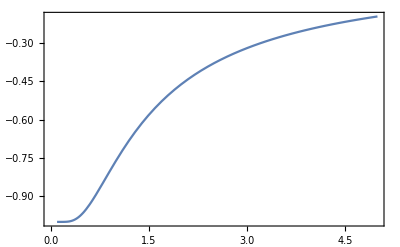

```mathematica
Plot[- Tanh[1/x],{x,0.1,5},AxesOrigin->{0,-1},Frame->True]
```

```mathematica
Cosh[0]
```

1

```mathematica
Clear[B]
```

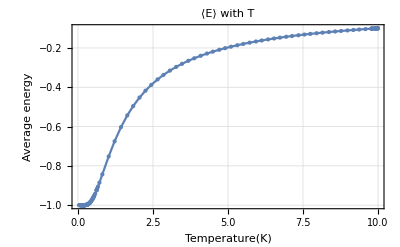

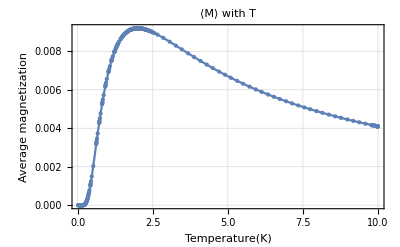

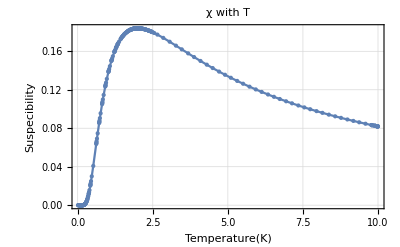

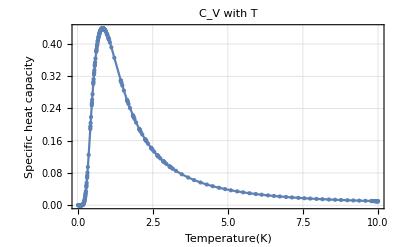

```mathematica
B=0.05;J=-1;
f1=Plot[-J Tanh[J/x],{x,0.01,10},AxesOrigin->{0,-1},Frame->True,PlotLabel->"⟨Ε⟩ with T",FrameLabel->{"Temperature(K)","Average energy"},Mesh->All,GridLines->Automatic,FrameTicks->None]
f2=Plot[Sinh[B/T]/(√(Sinh[B/T]^2+Exp[-4 J/T])),{T,0.01,10},Frame->True,PlotLabel->"⟨Μ⟩ with T",FrameLabel->{"Temperature(K)","Average magnetization"},Mesh->All,GridLines->Automatic,FrameTicks->None]
f3=Plot[(Exp[-4 J/T] Cosh[B/T])/(T (Sinh[B/T]^2+Exp[-4  J/T])^(3/2)),{T,0.01,10},Frame->True,PlotLabel->"χ with T",FrameLabel->{"Temperature(K)","Suspecibility"},Mesh->All,GridLines->Automatic,FrameTicks->None]

f4=Plot[(J^2 Sech[J/T]^2)/T^2,{T,0.01,10},Frame->True,PlotLabel->"C_V with T",FrameLabel->{"Temperature(K)","Specific heat capacity"},Mesh->All,GridLines->Automatic,FrameTicks->None]
```

```mathematica
Export["C:\Users\User\Desktop\任务\Computional-Physics\Report\Diagrams\analytic specific heat(j=1).pdf",f4]
```

C:\Users\User\Desktop\任务\Computional-Physics\Report\Diagrams\analytic specific heat(j=1).pdf

```mathematica
"C:\\Users\\User\\Desktop\\任务\\Computional-Physics\\Report\\Diagrams\\analytic average energy(j=1).pdf"
```

```mathematica
Tanh[-1]//N
```

-0.761594